## Mecánica Vectorial - Tarea 1 (Posición, velocidad, aceleración) - Briones Andrade Joshua

2) Sea el vector posición r⃗que varia con respecto el tiempo de la siguiente forma.

r⃗(t)=( Cos (ω t), e^(ω t) )

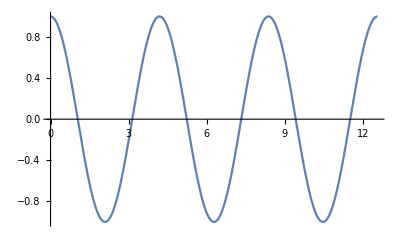

```mathematica
R1x =Plot[Cos[ω*t ]/.ω->1,{t,0, 4 Pi}]
```

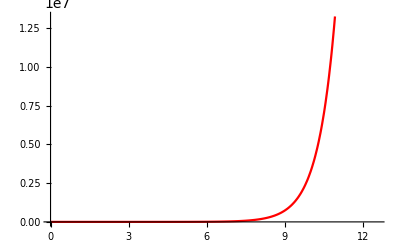

```mathematica
R1y= Plot[Exp[ω*t]/. ω->Pi /4,{t,0, 4 Pi}, PlotStyle->Red]
```

La velocidad de las componentes de R esta definida como la derivada con respecto al tiempo de sus componentes entonces tenemos lo siguiente.

OverVector[V(t)]= (d OverVector[r(t)])/dt= d/dt( Cos (ωt),e^ωt)= ( (d(Cos (ωt)))/dt,(d(e^ωt))/dt)=(-Sin (ωt)ωt/dt ,  e^ωt ωt/dt)=(-ω Sin (ωt) ,  ω e^ωt)= V⃗(t)

```mathematica
V1x=Plot[-Sin[ω t]*ω/. ω->Pi/4, {t,0,4 Pi}];
```

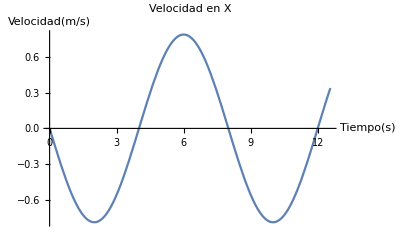

```mathematica
Show[V1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[HoldForm[Velocidad[m/s]]]},PlotLabel->"Velocidad en X" ]
```

```mathematica
V1y= Plot[Exp[ω*t]*ω/. ω->Pi/4,{t,0, 4 Pi}, PlotStyle->Red];
```

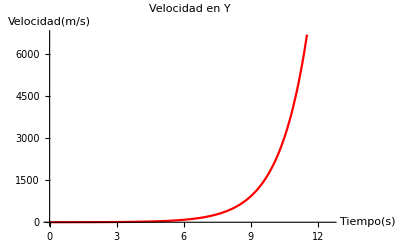

```mathematica
Show[V1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Velocidad[m/s]]},PlotLabel->HoldForm[Velocidad en Y],LabelStyle->{GrayLevel[0]}]
```

Continuamos ahora con la aceleración.

a⃗= (d V⃗)/dt= d/dt( -ω Sin(ω t),ω e^(ω t))= ( (d(-ω Sin(ω t)))/dt,(d(ω e^(ω t)))/dt)=(-ω^2 Cos(ω t) ,  ω^2 e^(ω t))= a⃗

```mathematica
A1x=Plot[-Cos[ω*t]*ω^2/. ω->Pi/4, {t,0,4 Pi}];
```

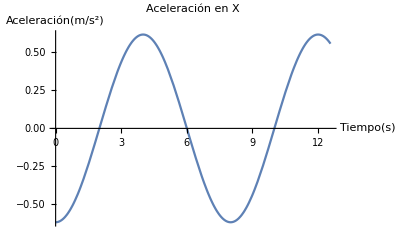

```mathematica
Show[A1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en X],LabelStyle->{GrayLevel[0]}]
```

```mathematica
A1y=Plot[Exp[ω *t]*ω^2/. ω->Pi/4, {t,0,4 Pi},PlotStyle->Red];
```

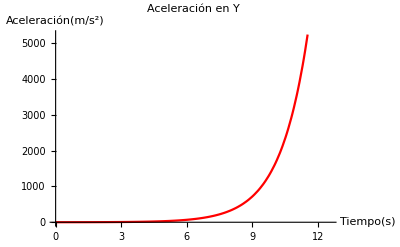

```mathematica
Show[A1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en Y],LabelStyle->{GrayLevel[0]}]
```